## Task 1 : Bases of vector spaces

#### 1.

```mathematica
coeff[f_,ip_,basis_]:=Module[{A,b,l},
l=Dimensions[basis][[1]];
A=Table[ip[basis[[i]],basis[[j]]],{i,1,l},{j,1,l}];
b=Table[ip[f,basis[[i]]],{i,1,l}];
Inverse[A].b//Simplify]
```

#### 2.

```mathematica
p={5,4};
q1={1,2};
q2={3,2};
S={q1,q2};
ip[a_,b_]:=a.b
```

```mathematica
c=coeff[p,ip,S];
Print["coefficience = ",c]
coeff[p,ip,S].S==p
```

coefficience = {1/2,3/2}

True

#### 3.

```mathematica
x1=-1;x2=1;
```

```mathematica
Clear[f]
Clear[ip]
```

```mathematica
f=2-x+x^2;
```

```mathematica
ip[a_,b_]:=Integrate[a b,{x,x1,x2}]
```

coefficience with respect to G = {6,-3,-1}

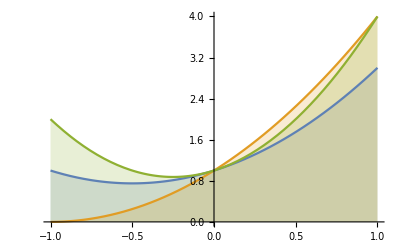

```mathematica
G={1+x+x^2,1+2x+x^2,1+x+2x^2};
cG=coeff[f,ip,G];
Print["coefficience with respect to G = ",cG]
pG=Plot[G,{x,-1,1},Filling->Axis]
```

coefficience with respect to H = {4,2,-1}

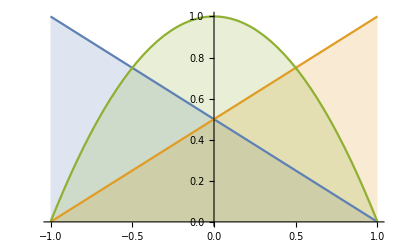

```mathematica
H={1/2 (1-x),1/2 (1+x),1-x^2};
cH=coeff[f,ip,H];
Print["coefficience with respect to H = ",cH]
pH=Plot[H,{x,-1,1},Filling->Axis]
```

#### 4.

```mathematica
Clear[H,G,f]
```

```mathematica
f=E^(-4x^2);
```

```mathematica
p=6;
```

```mathematica
basis[p_]:=Table[x^(i-1),{i,p+1}];
```

```mathematica
fwave[f_,ip_,basis_]:=basis.coeff[f,ip,basis]
```

```mathematica
fapp=Table[fwave[f,ip,basis[p]],{p,1,6}]//N
```

{0.441041,0.794189-1.05945 x^2,0.794189-1.05945 x^2,0.942396-2.54152 x^2+1.72908 x^4,0.942396-2.54152 x^2+1.72908 x^4,0.987119-3.48069 x^2+4.5466 x^4-2.06618 x^6}

```mathematica
Pl=Table[Plot[fapp[[i]],{x,-1,1}],{i,Length[fapp]}];
```

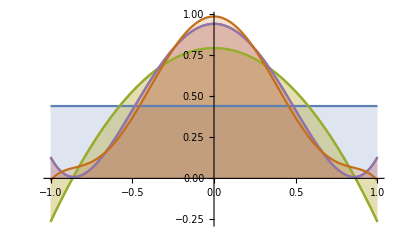

```mathematica
Plot[Evaluate[Table[fapp[[i]],{i,1,6}]],{x,-1,1},Filling->Axis]
```

```mathematica
err=NIntegrate[(f-fapp)^2, {x,-1,1}]
```

{0.237584,0.0380414,0.0380414,0.00333078,0.00333078,0.000179853}

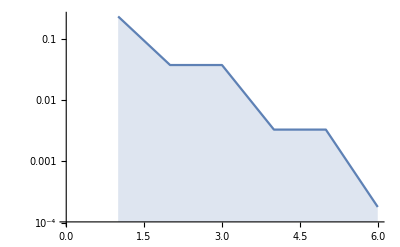

```mathematica
ListLogPlot[err,Joined->True,Filling->Axis]
```

#### 5.

```mathematica
Clear[ip,f,err,basis,fwave]
```

```mathematica
ipH1[a_,b_]:=Integrate[a b + D[a,x] D[b,x],{x,-1,1}]
ipL2[a_,b_]:=Integrate[a b ,{x,-1,1}]
```

```mathematica
basis[p_]:=Table[x^(i-1),{i,p+1}];
```

```mathematica
fwave[f_,ip_,basis_]:=basis.coeff[f,ip,basis]
```

```mathematica
f=E^(-4 x^2);
```

```mathematica
p=4;
```

```mathematica
fL2=fwave[f,ipL2,basis[p]]//N
```

0.942396-2.54152 x^2+1.72908 x^4

```mathematica
fH1=fwave[f,ipH1,basis[p]]//N
```

0.901963-2.1316 x^2+1.24806 x^4

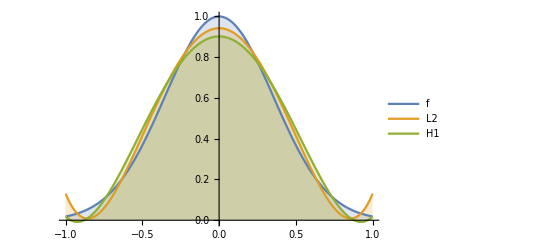

```mathematica
Plot[{f,fL2,fH1},{x,-1,1},PlotLegends->{"f","L2","H1"},Filling->Axis]
```

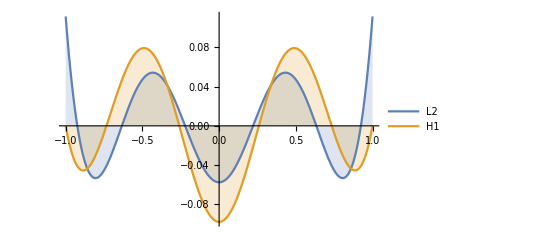

```mathematica
Plot[{fL2-f,fH1-f},{x,-1,1},PlotLegends->{"L2","H1"},Filling->Axis]
```

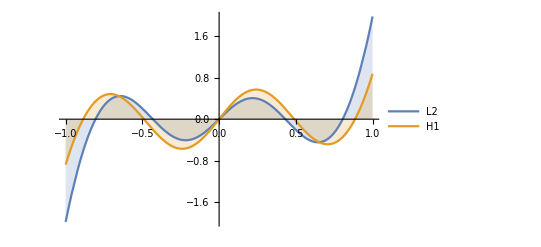

```mathematica
d1=D[fL2,x]-D[f,x];
d2=D[fH1,x]-D[f,x];
Plot[{d1,d2},{x,-1,1},PlotLegends->{"L2","H1"},Filling->Axis]
```

```mathematica
ClearAll
```

ClearAll

## Task 2: Linear independence

#### 1.

```mathematica
func[ip_,basis_]:=Module[{l,A},
l=Dimensions[basis][[1]];
A=Table[ip[basis[[i]],basis[[j]]],{i,1,l},{j,1,l}];
l==MatrixRank[A]]
```

#### 2.

```mathematica
ip[a_,b_]:=a.b
```

```mathematica
basis={{1,2},{4,2},{2,1}};
```

```mathematica
func[ip,basis]
```

False

#### 3.

```mathematica
Clear[basis,ip]
```

```mathematica
basis[p_]:=Table[x^(i-1),{i,p+1}];
```

```mathematica
ip[a_,b_]:=Integrate[a b,{x,-1,1}]
```

```mathematica
p=10;
```

```mathematica
Table[func[ip,basis[p]],{p,1,6}]
```

{True,True,True,True,True,True}